# Mathematica as a Tool for Astronomy and Physics

## Lecture 2 Wintersemester 2009/10 Markus Röllig

## Mathematica Conventions

### Naming

Required reading :

Naming Conventions

Without exception, all Mathematica Functions and pre-defined Symbols start with a capital Letter.

```mathematica
sin[x]
Sin[x]
Sin(x)
```

sin[x]

Sin[x]

Sin x

Starting with Version 6.0 Mathematica introduced format highlighting. The above cell demonstrates this. Symbols (Commands, Variables, etc.) that are known to the kernel are shown black. Unknown symbols are printed blue (here the x is undefined, hence blue and the sin is also unknown to Mathematica). Obvious typing errors show up in red (round brackets instead of the expected square brackets [ ] to indicate a function argument).

Most  Mathematica commands usually are spelled out complete English words.

```mathematica
Integrate[1/(x^3+1),{x,0,1}]
```

1/18 (2 √3 π+Log[64])

If the command consists of multiple word, each one starts with a capital letter.

```mathematica
RandomInteger[100000]
```

33620

```mathematica
IntegerDigits[123456789]
```

{1,2,3,4,5,6,7,8,9}

```mathematica
FixedPointList[Cos[#]&,1.]
```

{1.,0.540302,0.857553,0.65429,0.79348,0.701369,0.76396,0.722102,0.750418,0.731404,0.744237,0.735605,0.741425,0.737507,0.740147,0.738369,0.739567,0.73876,0.739304,0.738938,0.739184,0.739018,0.73913,0.739055,0.739106,0.739071,0.739094,0.739079,0.739089,0.739082,0.739087,0.739084,0.739086,0.739085,0.739086,0.739085,0.739085,0.739085,0.739085,0.739085,0.739085,0.739085,0.739085,0.739085,0.739085,0.739085,0.739085,0.739085,0.739085,0.739085,0.739085,0.739085,0.739085,0.739085,0.739085,0.739085,0.739085,0.739085,0.739085,0.739085,0.739085,0.739085,0.739085,0.739085,0.739085,0.739085,0.739085,0.739085,0.739085,0.739085,0.739085,0.739085,0.739085,0.739085,0.739085,0.739085,0.739085,0.739085,0.739085,0.739085,0.739085,0.739085,0.739085,0.739085,0.739085,0.739085,0.739085,0.739085,0.739085,0.739085,0.739085}

Use meaningful naming for your own variables and functions!

### Brackets

In Mathematica the following brackets are used:

( )	to control the order of calculations,
[ ]  	to indicate the argument or arguments of a function,
{ } 	to indicate a list, a group of elements,
⟦ ⟧ 	to indicate the element number in the list, the index.
	can by typed also as [[ ]]

```mathematica
1/(1+2+x^2+x^3)
```

1/(3+x^2+x^3)

```mathematica
a/(b c)
a/b c
```

a/(b c)

(a c)/b

```mathematica
{a,b,c,d}⟦2⟧
{a,b,c,d}[[2]]
```

b

b

#### Excercise

Use the keyboard to enter ⟦ ⟧

### Input Defaults

By default a new cell will be an input cell unless you selected a different cell style before creating the cell. An input cell interprets anything as interpretable expression. If you want to write comments or text use either a text cell or use comment brackets (* ...*). Everything between the (* ... *) will be ignored and greyed out. Comments can span many lines (but not many cells).
Example:

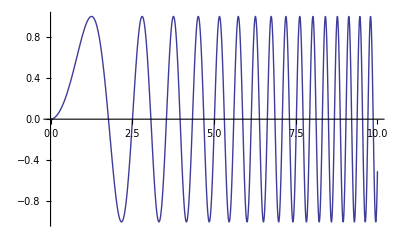

```mathematica
Plot[Sin[x^2],{x,0,10}] (* a simple plot *)
```

Comment blocks can be inserted at any position of a Mathematica expression as long as the expression names are untouched:.

```mathematica
Integrate(*test*)[(*test*)x,x(*test*)]
```

x^2/2

```mathematica
Integr(*test*)ate
```

ate Integr

### In/Output, Sequence of Inputs

Required reading:

Sequences of Operations

Most Mathematica input creates an output. If you want to supress outputs use semicolon ; after the expression:

```mathematica
a+2+f+g+t+4;
```

```mathematica
Plot[Sin[x]^3/(1+x^2 Cos[√x])Log[x],{x,1,17}];
```

Please note, that Mathematica assumes that a semicolon after a Plot is unwanted and accordingly highlights it red.

If you want to use more then one expression in one line use ; but note, that only the last expression produces an output.

```mathematica
a+b+c+d+e;1+2+3+4+5;√13.8764831276
```

3.72512

If you want the output of intermediary expressions vissible you can use Print.

```mathematica
a+b+c+d+e;Print[a+b+c+d+e];1+2+3+4+5;√13.8764831276
```

a+b+c+d+e

3.72512

You can not use Print[%]:

```mathematica
a+b+c+d+e;Print[%];1+2+3+4+5;√13.8764831276
```

3.72512

3.72512

## Lists

Required Reading

Lists

In doing calculations, it is often convenient to collect together several objects, and treat them as a single entity. Lists give you a way to make collections of objects in Mathematica. As you will see later, lists are very important and general structures in Mathematica.

### Overview

Lists in Mathematica are delimited by curly braces, with elements separated by commas. They can contain any valid Mathematica expression: numbers, strings, symbols, graphics, ... basically anything.
When a list is constructed, each element is evaluated and the corresponding entry is filled with that value. 
List expressions have List as their Head.

```mathematica
{a,b,c,d}   (* a List *)
Head[{a,b,c,d}]    (* Show the Head of the List *)
FullForm[{a,b,c,d}]     (* Show the Full Form of the list *)
List[a,b,c,d] 
Length[%]     (* give the length of the list *)
```

{a,b,c,d}

List

List[a,b,c,d]

{a,b,c,d}

4

In many ways you can treat lists as single objects. Many Mathematica operations work on whole lists.

```mathematica
{3,5,1}
```

{3,5,1}

```mathematica
{3,5,1}^2
```

{9,25,1}

```mathematica
v={2,4,3.1}
v/(v-1)
Clear[v]
```

{2,4,3.1}

{2,4/3,1.47619}

```mathematica
{3,5,1}
```

{3,5,1}

```mathematica
x^%-1
```

{-1+x^3,-1+x^5,-1+x}

### Creating Lists

Required Reading :

Constructing Lists

You can create lists in many ways. Of course you can directly type in lists:

```mathematica
{1,2,3,4,5,6,7,8,9}
{"a","b","c","d","e","f","g","h","i","j"}
```

{1,2,3,4,5,6,7,8,9}

{a,b,c,d,e,f,g,h,i,j}

There are programmatic ways to create the same lists:

```mathematica
Range[9]
CharacterRange["a","j"]
```

{1,2,3,4,5,6,7,8,9}

{a,b,c,d,e,f,g,h,i,j}

Range[i_min,i_max,di]  generates the list {i_min,…,i_max} using step di. i_min and di are by default 1. 

CharacterRange["c_1","c_2"] yields a list of the characters in the range from "c_1" to "c_2",

Other (more flexible) ways are:

```mathematica
Table[i,{i,9}]
Array[#1&,9]
```

{1,2,3,4,5,6,7,8,9}

{1,2,3,4,5,6,7,8,9}

One of the most important commands to set up lists is Table. 
The standard syntax is Table[expr,{i,i_min,i_max}].

```mathematica
Table[2,{i,0,10}]
```

{2,2,2,2,2,2,2,2,2,2,2}

```mathematica
Table[2^i,{i,0,10}]
```

{1,2,4,8,16,32,64,128,256,512,1024}

The table index can have symbolic values:

```mathematica
Table[2^x+x,{x,a,a+5n,n}]
```

{2^a+a,2^(a+n)+a+n,2^(a+2 n)+a+2 n,2^(a+3 n)+a+3 n,2^(a+4 n)+a+4 n,2^(a+5 n)+a+5 n}

Table can swallow any expression. This makes it one of the most important and powerful commands

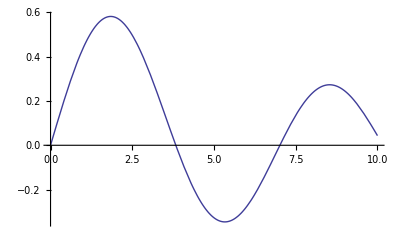
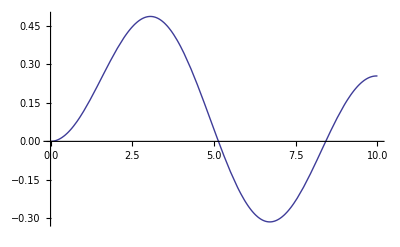
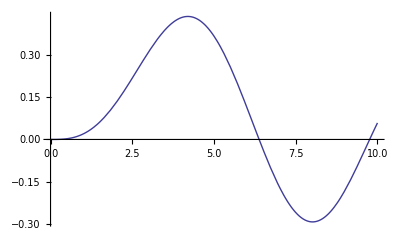
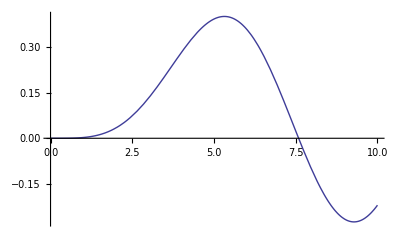

```mathematica
Table[Plot[BesselJ[n,x],{x,0,10}],{n,4}]
```

```mathematica
Column[Table[Binomial[i,j],{i,0,8},{j,0,i}],Center]
```

{1}
{1,1}
{1,2,1}
{1,3,3,1}
{1,4,6,4,1}
{1,5,10,10,5,1}
{1,6,15,20,15,6,1}
{1,7,21,35,35,21,7,1}
{1,8,28,56,70,56,28,8,1}

```mathematica
Table[Style["text", s], {s, 10, 20}]
```

{text,text,text,text,text,text,text,text,text,text,text}

Table can also loop over any arbitrary list of successive values: Table[expr,{i,{i_1,i_2,…}}]

```mathematica
Table[Log[2,i],{i,Table[2^i,{i,0,10}]}]
```

{0,1,2,3,4,5,6,7,8,9,10}

You can also build up lists of lists (i.e matrices/arrays) by using nested tables:

```mathematica
Table[Table[a[i,j],{j,1,4}],{i,1,3}]
%//MatrixForm
```

{{a[1,1],a[1,2],a[1,3],a[1,4]},{a[2,1],a[2,2],a[2,3],a[2,4]},{a[3,1],a[3,2],a[3,3],a[3,4]}}

(a[1,1] | a[1,2] | a[1,3] | a[1,4]
a[2,1] | a[2,2] | a[2,3] | a[2,4]
a[3,1] | a[3,2] | a[3,3] | a[3,4])

Nested tables can be entered directly as:
(notice the ordering of the running indices. German Merkregel: "Zeilen zuerst, Spalten später")

```mathematica
Table[a[i,j],{i,1,3},{j,1,4}]//MatrixForm
```

(a[1,1] | a[1,2] | a[1,3] | a[1,4]
a[2,1] | a[2,2] | a[2,3] | a[2,4]
a[3,1] | a[3,2] | a[3,3] | a[3,4])

```mathematica
Array[a[##]&,{3,4}]//MatrixForm
```

(a[1,1] | a[1,2] | a[1,3] | a[1,4]
a[2,1] | a[2,2] | a[2,3] | a[2,4]
a[3,1] | a[3,2] | a[3,3] | a[3,4])

There many ways of generating lists in Mathematica. Some of them are optimized for speed:

```mathematica
Table[i,{i,10^8}];//AbsoluteTiming
```

{3.2916,Null}

```mathematica
Range[10^8];//AbsoluteTiming
```

{0.468,Null}

```mathematica
Array[#&,10^8];//AbsoluteTiming
```

{3.2448,Null}

Tuples[list,n] generates a list of all possible n-tuples of elements from list.

```mathematica
Tuples[{0,1},3]
```

{{0,0,0},{0,0,1},{0,1,0},{0,1,1},{1,0,0},{1,0,1},{1,1,0},{1,1,1}}

```mathematica
Tuples[{a,b},2]
```

{{a,a},{a,b},{b,a},{b,b}}

2D lattice of points:

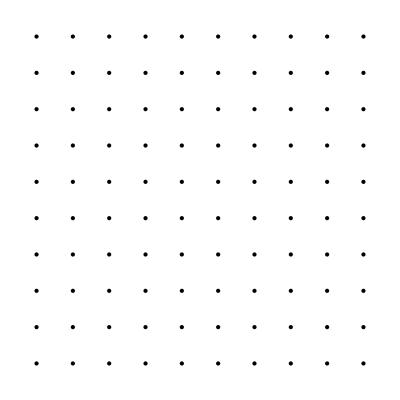

```mathematica
Graphics[Point[Tuples[Range[0,9],2]]]
```

3D lattice of points:

```mathematica
Graphics3D[{PointSize[0],Point[Tuples[Range[0,9],3]]}]
```

-Graphics3D-

#### Excercises

Enter the 4x4 identity matrix.

Type in and calculate {a,b,c}.{x,y,z} using both the operator form and the function form (Dot)

Create a list of 100 random integers between 1 and 10.

Create a list of 100 random reals between 1 and 5.

Create a list of the first 50 powers to the base 2.

Create a list of the first 20 Fibonacci numbers.

Plot the first 50 Primes using ListPlot.

Produce a list of numbers between 0.15 and 1.25 with a spacing of 0.1.

Produce a list of the first 10 Legendre polynomials.  Use the formatting function ColumnForm to improve the appearance of your output.

### Elements of Lists

To access elements of a list use the command Part[expr,i]

```mathematica
Part[{a,b,c,d,e,f,g,h,i,j},5]
```

e

The shortcut notation is expr[[i]]

```mathematica
{a,b,c,d,e,f,g,h,i,j}[[5]]
```

e

The index i can also be negative, counting from the end

```mathematica
{a,b,c,d,e,f,g,h,i,j}[[1]]
{a,b,c,d,e,f,g,h,i,j}[[-1]]
```

a

j

Part[list,{i,j,…}]  or  list[[{i,j,…}]] extracts a list of elements

```mathematica
{a,b,c,d,e,f,g,h,i,j}[[{4,5,6}]]
```

{d,e,f}

You can even extract a Span of elements i through j using i;;j : Part[list,i;;j]

```mathematica
{a,b,c,d,e,f,g,h,i,j}[[4;;6]] 
(* note that no curly list brackets are used her *)
```

{d,e,f}

Multidimensional lists are accessed with Part[expr,i,j,…] or expr[[i, j, …]] (shortcut for expr[[i]][[j]]…. ). You can also use All to specifiy all parts of a dimension.

```mathematica
l=Table[a[i,j],{i,1,3},{j,1,4}];
```

```mathematica
l[[1]] (* extracts a row *)
```

{a[1,1],a[1,2],a[1,3],a[1,4]}

```mathematica
l[[All,1]] (*extracts the first column *)
```

{a[1,1],a[2,1],a[3,1]}

```mathematica
l[[1,1]] (* extracts single elements *)
```

a[1,1]

```mathematica
l[[1;;2,2;;3]]  (*extract a submatrix *)
```

{{a[1,2],a[1,3]},{a[2,2],a[2,3]}}

```mathematica
Clear[l];
```

Partcan also be used to assign new values to parts of a list

```mathematica
l=Range[10]
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
l[[5]]=1000;
l
```

{1,2,3,4,1000,6,7,8,9,10}

```mathematica
Clear[l];
```

Take[list,n]gives the first n elements of list. If n is negative it gives the last n elements of a list.

```mathematica
Take[Range[10],-3]
```

{8,9,10}

Take works with any head, not just List:

```mathematica
Take[a+b+c+d+e+f,3]
```

a+b+c

Drop[list,n]is the opposite and gives list with the first n elements dropped.

```mathematica
Drop[{a,b,c,d,e,f},2]
```

{c,d,e,f}

There are also some special commands for common list extraction tasks

```mathematica
First[{a,b,c,d,e,f}]
```

a

```mathematica
Last[{a,b,c,d,e,f}]
```

f

```mathematica
Most[{a,b,c,d,e,f}]
```

{a,b,c,d,e}

```mathematica
Rest[{a,b,c,d,e,f}]
```

{b,c,d,e,f}

Check the following documentation page for some more commands:

Parts of Matrices

#### Excercises

Given the list {"A", "B", "C", "D", "E", "F", "G", "H", "I", "J", "K", "L", "M", "N", "O", "P", "Q", "R", "S", "T", "U", "V", "W", "X", "Y", "Z"}, extract 
a) every second element.
b) every fourth element
c) the elements number 2,12,13,18
d) the first 20 elements
e) elements from "J" to "P"

### Searching and Testing Lists

#### Identify Lists

```mathematica
?ListQ
```

RowBox[{"ListQ", "[", StyleBox["expr", "TI"], "]"}] gives True if StyleBox["expr", "TI"] is a list, and False otherwise.

```mathematica
ListQ[{1,2,3,4,5,6,7,8}]
```

True

```mathematica
ListQ[{{a,b},{c,d}}]
```

True

```mathematica
ListQ[{{a,b},{c,d},{e},{"f","g","h"}}]
```

True

```mathematica
ListQ[Sin[x]]
```

False

```mathematica
?VectorQ
```

RowBox[{"VectorQ", "[", StyleBox["expr", "TI"], "]"}] gives True if StyleBox["expr", "TI"] is a list or a one-dimensional SparseArray object, none of whose elements are themselves lists, and gives False otherwise. 
RowBox[{"VectorQ", "[", RowBox[{StyleBox["expr", "TI"], ",", StyleBox["test", "TI"]}], "]"}] gives True only if StyleBox["test", "TI"] yields True when applied to each of the elements in StyleBox["expr", "TI"].

```mathematica
?MatrixQ
```

RowBox[{"MatrixQ", "[", StyleBox["expr", "TI"], "]"}] gives True if StyleBox["expr", "TI"] is a list of lists or a two-dimensional SparseArray object that can represent a matrix, and gives False otherwise. 
RowBox[{"MatrixQ", "[", RowBox[{StyleBox["expr", "TI"], ",", StyleBox["test", "TI"]}], "]"}] gives True only if StyleBox["test", "TI"] yields True when applied to each of the matrix elements in StyleBox["expr", "TI"].

```mathematica
VectorQ[{1,2,3,4,5,6,7,8}]
MatrixQ[{1,2,3,4,5,6,7,8}]
```

True

False

```mathematica
VectorQ[{{a,b},{c,d}}]
MatrixQ[{{a,b},{c,d}}]
```

False

True

```mathematica
VectorQ[{{a,b},{c,d},{e},{"f","g","h"}}]
MatrixQ[{{a,b},{c,d},{e},{"f","g","h"}}]
```

False

False

In a full array all parts at a particular level must be lists of the same length.

```mathematica
?ArrayQ
```

RowBox[{"ArrayQ", "[", StyleBox["expr", "TI"], "]"}] gives True if StyleBox["expr", "TI"] is a full array or a SparseArray object, and gives False otherwise. 
RowBox[{"ArrayQ", "[", RowBox[{StyleBox["expr", "TI"], ",", StyleBox["patt", "TI"]}], "]"}] requires StyleBox["expr", "TI"] to be a full array with a depth that matches the pattern StyleBox["patt", "TI"]. 
RowBox[{"ArrayQ", "[", RowBox[{StyleBox["expr", "TI"], ",", StyleBox["patt", "TI"], ",", StyleBox["test", "TI"]}], "]"}] requires also that StyleBox["test", "TI"] yield True when applied to each of the array elements in StyleBox["expr", "TI"].

```mathematica
ArrayQ[{1,2,3,4}]
```

True

```mathematica
ArrayQ[{1,2,{3},4}]
```

False

#### Describe Lists

```mathematica
Length[{1,2,3,4,5,6,7,8}]
```

8

```mathematica
Length[{{1,2,3,4,5,6,7,8},{a,b,c,d,e,f,g,h}}]
```

2

```mathematica
Dimensions[{{1,2,3,4,5,6,7,8},{a,b,c,d,e,f,g,h}}]
```

{2,8}

```mathematica
?ArrayDepth
```

RowBox[{"ArrayDepth", "[", StyleBox["expr", "TI"], "]"}] gives the depth to which StyleBox["expr", "TI"] is a full array, with all the parts at a particular level being lists of the same length, or is a SparseArray object.

ArrayDepth[expr] gives the depth to which expr is a full array, with all the parts at a particular level being lists of the same length, or is a SparseArray object.

```mathematica
ArrayDepth[{{a, b}, {c, d}}]
```

2

```mathematica
ArrayDepth[{{a, b}, {c}}]
```

1

It is also possible to checkt whether particular elements/expressions are member of the list using MemberQ[list,form]. The opposite check is also possible: FreeQ[expr,form]

```mathematica
MemberQ[{1, 3, 4, 1, 2}, 2]
```

True

MemberQ normally only tests level 1:

```mathematica
MemberQ[{{1, 1, 3, 0}, {2, 1, 2, 2}}, 0]
```

False

Test down to level 2 :

```mathematica
MemberQ[{{1, 1, 3, 0}, {2, 1, 2, 2}}, 0, 2]
```

True

```mathematica
FreeQ[{1, 2, 4, 1, 0}, 0]
```

False

FreeQ normally tests all levels in an expression:

FreeQ[{{1, 1, 3, 0}, {2, 1, 2, 2}}, 0]

Example Applications :
  
  Test which integrals are free of logarithms :

```mathematica
Table[FreeQ[Integrate[x^n, x], Log], {n, -5, 5}]
```

{True,True,True,True,False,True,True,True,True,True,True}

#### Search List Elements

Find the positions at which b occurs:

```mathematica
Position[{a,b,a,a,b,c,b},b]
```

{{2},{5},{7}}

```mathematica
Position[{{a,a,b},{b,a,a},{a,b,a}},b]
```

{{1,3},{2,1},{3,2}}

Find the positions of the first 2 b's that appear on level 1:

```mathematica
Position[{a,b,a,a,b,c,b,a,b},b,1,2]
```

{{2},{5}}

Extract the second part from an expression :

```mathematica
Extract[{1,2,3,4},{2}]
```

2

#### Excercises

Obtain a (partial) list of query functions ending in Q.  Try a few.

Given a long list of 1000 random integers between 1 and 20, find the positions of the first 10 1's.

Given a long list of 1000 random integers between 1 and 20, find the positions of the first 10 even numbers.

Given a long list of 1000 random integers between 1 and 20,extract first 20 uneven numbers.

### Adding, Removing and Modifying List Elements

Required Reading:

Adding, Removing and Modifying List Elements

Important commands are: Prepend, Append, Insert, AppendTo, and PrependTo

```mathematica
Prepend[{1,2,3,4},0]
```

{0,1,2,3,4}

```mathematica
Append[{1,2,3,4},5]
```

{1,2,3,4,5}

```mathematica
Insert[{1,2,3,4},2.5,3]
```

{1,2,2.5,3,4}

These commands do not change the original expression!

```mathematica
list={1,2,3,4,5};
Prepend[list,x]
list
```

{x,1,2,3,4,5}

{1,2,3,4,5}

AppendTo, and PrependTo will do that

```mathematica
list={1,2,3,4,5};
PrependTo[list,x]
list
```

{x,1,2,3,4,5}

{x,1,2,3,4,5}

```mathematica
Clear[list,x]
```

Delete[list,i] deletes the element at position i.

```mathematica
Delete[{1,2,3,4,5,6,7,8,9},5]
```

{1,2,3,4,6,7,8,9}

ReplacePart[list,i->new] replace the element at position i in list with new

```mathematica
ReplacePart[{a,b,c,d},3->x]
```

{a,b,x,d}

### Rearranging Lists

Mathematica offers many built in solutions for common rearranging tasks. Some typical examples are given below. If you want to learn more about them, study their respective Help pages.

```mathematica
Sort[{3,5,7,32,5,6,8,9,3,2,4,7,9}]
```

{2,3,3,4,5,5,6,7,7,8,9,9,32}

You can also use Union[list]to sort elements, but this removes any duplicates

```mathematica
Union[{3,5,7,32,5,6,8,9,3,2,4,7,9}]
```

{2,3,4,5,6,7,8,9,32}

```mathematica
Reverse[{1,2,3,4,5,6,7,8,9}]
```

{9,8,7,6,5,4,3,2,1}

```mathematica
RotateLeft[{a,b,c,d,e},2]
```

{c,d,e,a,b}

```mathematica
RotateLeft[{a,b,c,d,e},-2]
RotateRight[{a,b,c,d,e},2]
```

{d,e,a,b,c}

{d,e,a,b,c}

To combine multiple list into one you can use:
Join[list_1,list_2,…] to concatenate lists together
and Riffle[list_1,list_2]to interleave elements of list_1 and list_2

```mathematica
Join[{a,b,c,d},{e,f,g,h,i}]
```

{a,b,c,d,e,f,g,h,i}

Join leaves the elements untouched.

```mathematica
Join[{a,b,c,d},{d,e,f,g,h,i}]
```

{a,b,c,d,d,e,f,g,h,i}

```mathematica
Riffle[{a,b,c},{x,y,z}]
```

{a,x,b,y,c,z}

Riffle cycles through the elements of the second list, if the Lengths of both lists differ.

```mathematica
Riffle[{a,b,c,d},{x,y}]
```

{a,x,b,y,c,x,d}

```mathematica
Riffle[{a,b,c},{x}]
```

{a,x,b,x,c}

#### Rearranging Nested Lists

You will often encounter nested lists. Handling such lists can be done for instance like this:
Transpose[list]	interchange the top two levels of lists

```mathematica
{{1,2,3},{4,5,6}}//MatrixForm
Transpose[{{1,2,3},{4,5,6}}]//MatrixForm
```

(1 | 2 | 3
4 | 5 | 6)

(1 | 4
2 | 5
3 | 6)

```mathematica
Flatten[{d,{c,{b,{a}}}}]
```

{d,c,b,a}

Flatten[list,n] flatten out the top n levels in list

```mathematica
Flatten[{{{{a}}}}]
```

{a}

```mathematica
Flatten[{{{{a}}}},1]
Flatten[{{{{a}}}},2]
Flatten[{{{{a}}}},3]
```

{{{a}}}

{{a}}

{a}

But you have to be careful not to destroy meaningfull nesting.

```mathematica
Flatten[{{{x,y},{1,2}}}]
```

{x,y,1,2}

To keep the {x,y} pairs:

```mathematica
Flatten[{{{x,y},{1,2}}},1]
```

{{x,y},{1,2}}

You can partition lists

```mathematica
Partition[{1,2,3,4,5,6,7,8,9},3]
```

{{1,2,3},{4,5,6},{7,8,9}}

But Partition throws away elements that don't exactly fit into the partition scheme:

```mathematica
Partition[{1,2,3,4,5,6,7,8,9,10},3]
```

{{1,2,3},{4,5,6},{7,8,9}}

```mathematica
Partition[PadRight[{1,2,3,4,5,6,7,8,9,10},12],3]
Partition[PadRight[{1,2,3,4,5,6,7,8,9,10},12,x],3]
```

{{1,2,3},{4,5,6},{7,8,9},{10,0,0}}

{{1,2,3},{4,5,6},{7,8,9},{10,x,x}}

#### Lists as Sets

Mathematica usually keeps the elements of a list in exactly the order you originally entered them. If you want to treat a Mathematica list like a mathematical set, however, you may want to ignore the order of elements in the list.

```mathematica
Union[{1,2,3,4},{2,3,4,5},{a,b,c}]
```

{1,2,3,4,5,a,b,c}

```mathematica
Intersection[{1,2,3,4},{2,3,4,5},{a,b,c}]
```

{}

```mathematica
Intersection[{1,2,3,4},{2,3,4,5}]
```

{2,3,4}

Intersection does not care about the order of list arguments. The opposite process however, does:

```mathematica
Complement[{1,2,3,4},{2,3,4,5}]
Complement[{2,3,4,5},{1,2,3,4}]
```

{1}

{5}

Complement[universal,list_1,…]	give a list of the elements that are in universal, but not in any of the list_i

```mathematica
DeleteDuplicates[{1,2,3,4,4,3,4,5,6,7}]
```

{1,2,3,4,5,6,7}

```mathematica
Union[{1,2,3,4,4,3,4,5,6,7}]
```

{1,2,3,4,5,6,7}

```mathematica
Subsets[{1,2,3}]
```

{{},{1},{2},{3},{1,2},{1,3},{2,3},{1,2,3}}

#### Excercise

Evaluate {a,b,c}.{x,y,z} using both the operator form and the function form (Dot)

Evaluate {{m11,m12,m13},{m21,m22,m23},{m31,m32,m33}}.{x,y,z} and interpret the result

Compute the eigenvalues of the matrix(1 | 2 | 3
4 | 5 | 6
7 | 8 | 9) using the built-in function Eigenvalues.

Create {x,y} lists:
Given two random x- and y- vector of dimension 10. Create the list of 10 {x,y} pairs.
Do the same for dimension of 1000 and visualize the list using ListPlot.
Create a similar vidualization of 3-dimensional {x,y,z} pairs.

Which numbers smaller than 1000 are Primes and Fibonacci numbers?

Given a list of 1000 {x,y,z} pairs, produce a list of {x,z} pairs, and give the y-vector.

```mathematica
xyzList=RandomReal[10,{1000,3}];
```